😫, now it is day 6.

```mathematica
input = "Time:        48     98     90     83
Distance:   390   1103   1112   1360";
```

## Part 1

```mathematica
inputParse = (Map[ToExpression,StringCases[#,RegularExpression["\\d+"]]& @input // Partition[#,4]&,2] )//  MapThread[<|"Time"-> #1,"Distance"->#2|>&, #]&
```

{<|Time→48,Distance→390|>,<|Time→98,Distance→1103|>,<|Time→90,Distance→1112|>,<|Time→83,Distance→1360|>}

We only need to abstract the problem we have to a linear algebra function

```mathematica
findPossibleSolution[{time_Integer,distance_Integer}] := Module[{speedChoice = Range[time]},
Echo[speedChoice,"Speed choices"];
remainingTime = ConstantArray[time,time] - speedChoice;
Echo[remainingTime,"Remaining time"];
solutions = MapThread[<|"SpeedChoice"-> #1, "Result"-> #1*#2|>&,{speedChoice,remainingTime}];
 Echo[solutions,"Avaiable solution"];
Select[solutions,#["Result"] >= distance &] // Length
]
```

```mathematica
findPossibleSolution[{inputParse[[1]]["Time"],inputParse[[4]]["Distance"]}]
```

Speed choices  {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

Remaining time  {47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

Avaiable solution  {<|SpeedChoice→1,Result→47|>,<|SpeedChoice→2,Result→92|>,<|SpeedChoice→3,Result→135|>,<|SpeedChoice→4,Result→176|>,<|SpeedChoice→5,Result→215|>,<|SpeedChoice→6,Result→252|>,<|SpeedChoice→7,Result→287|>,<|SpeedChoice→8,Result→320|>,<|SpeedChoice→9,Result→351|>,<|SpeedChoice→10,Result→380|>,<|SpeedChoice→11,Result→407|>,<|SpeedChoice→12,Result→432|>,<|SpeedChoice→13,Result→455|>,<|SpeedChoice→14,Result→476|>,<|SpeedChoice→15,Result→495|>,<|SpeedChoice→16,Result→512|>,<|SpeedChoice→17,Result→527|>,<|SpeedChoice→18,Result→540|>,<|SpeedChoice→19,Result→551|>,<|SpeedChoice→20,Result→560|>,<|SpeedChoice→21,Result→567|>,<|SpeedChoice→22,Result→572|>,<|SpeedChoice→23,Result→575|>,<|SpeedChoice→24,Result→576|>,<|SpeedChoice→25,Result→575|>,<|SpeedChoice→26,Result→572|>,<|SpeedChoice→27,Result→567|>,<|SpeedChoice→28,Result→560|>,<|SpeedChoice→29,Result→551|>,<|SpeedChoice→30,Result→540|>,<|SpeedChoice→31,Result→527|>,<|SpeedChoice→32,Result→512|>,<|SpeedChoice→33,Result→495|>,<|SpeedChoice→34,Result→476|>,<|SpeedChoice→35,Result→455|>,<|SpeedChoice→36,Result→432|>,<|SpeedChoice→37,Result→407|>,<|SpeedChoice→38,Result→380|>,<|SpeedChoice→39,Result→351|>,<|SpeedChoice→40,Result→320|>,<|SpeedChoice→41,Result→287|>,<|SpeedChoice→42,Result→252|>,<|SpeedChoice→43,Result→215|>,<|SpeedChoice→44,Result→176|>,<|SpeedChoice→45,Result→135|>,<|SpeedChoice→46,Result→92|>,<|SpeedChoice→47,Result→47|>,<|SpeedChoice→48,Result→0|>}

0

```mathematica
findPossibleSolution /@ ({#["Time"],#["Distance"]} & /@ inputParse) // Fold[Times,#]& //QuietEcho
```

4568778

## Part 2

Typical case of average algorithm problems, try to make the involve argument as much as big as possible

```mathematica
inputParse2 =ToExpression /@ (StringJoin/@(StringCases[#,RegularExpression["\\d+"]]& @input // Partition[#,4]&))
```

{48989083,390110311121360}

```mathematica
findPossibleSolution[inputParse2] //QuietEcho (* Memory suffered*)
```

Let go back, try the pattern of result and input in part 1

```mathematica
findPossibleSolution /@ ({#["Time"],#["Distance"]} & /@ inputParse) // QuietEcho
```

{27,73,61,38}

```mathematica
inputParse
```

{<|Time→48,Distance→390|>,<|Time→98,Distance→1103|>,<|Time→90,Distance→1112|>,<|Time→83,Distance→1360|>}

Let me see, I forget what name we should call this, ah single variable polynomial or something like that (I not good at math, so my name I give you may sound stupid, sorry folks 😆), a function that if we plot it will look like a mountain. Why, because I look at the distance pattern at part 1, it go up and down.  We have distance = remainingTime * speed, with remainingTime = (maximumTime - speed) . So we have function of single argument
d = (t - s)*s = st - s^2 .  
t (maximum time) is independent.
s (speed) from 0 to maximum time.

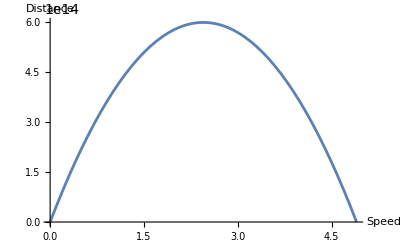

```mathematica
Plot[-s^2 + s* 48989083,{s,0,48989083},AxesLabel -> {"Speed","Distance"}]
```

It not hard to guest, what we find is 2 point of speed axis that wrap the area where the curve go beyond the required distance, like this:

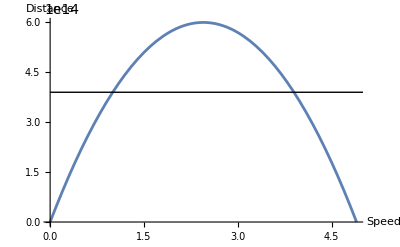

```mathematica
Show[Plot[-s^2 + s* 48989083, {s, 0, 48989083}, AxesLabel -> {"Speed", "Distance"}],
Epilog ->Line[{{0,inputParse2[[2]]},{inputParse2[[2]],inputParse2[[2]]}}]]
```

d = st - s^2 ⇔ 48989083 * s - s^2 - 390110311121360 = 0

```mathematica
Solve[ 48989083*s-s^2 - 390110311121360==0,{s}]
```

{{s→1/2 (48989083-√839489008695449)},{s→1/2 (48989083+√839489008695449)}}

```mathematica
N[{{s->1/2 (48989083-√839489008695449)},{s->1/2 (48989083+√839489008695449)}}]
```

{{s→1.00076×10^7},{s→3.89815×10^7}}

Hum, did I go wrong?, this numbers is so big, let check with smaller numbers of part 1.

```mathematica
inputParse[[1]]
```

<|Time→48,Distance→390|>

```mathematica
Solve[48*s -s^2- 390 == 0,{s}]
```

{{s→24-√186},{s→24+√186}}

```mathematica
test1 = N[{{s->24-√186},{s->24+√186}}]
```

{{s→10.3618},{s→37.6382}}

Okie, from 10.3 to 37.6 we have 27 integer numbers, that corrected. Let find a function that can extract only integers

```mathematica
Values[test1] // Flatten // #[[2]] -#[[1]] & // IntegerPart[#]&
```

27

```mathematica
IntegerPart[27.276363393971707]
```

27

Okie, let use this method

```mathematica
Solve[ 48989083*s-s^2 - 390110311121360==0,{s}] //N // Values // Flatten // #[[2]] -#[[1]] & // IntegerPart[#]&
```

28973936

Correct!, thank you for reading

## Scratchpad

```mathematica
SetDirectory["~/nhannht-projects/aoc2023"]
```

/home/vermin/nhannht-projects/aoc2023